# Practical 5 :

## Solution of one dimensional wave equation u_tt = c^2 u_xx, for finite string of length l, that is to solve the IBVP ; u_tt=c^2 u_xx , 0<x<l , t>0, u(x,0)=f(x),0≤x≤l, u_t(x,0)=g(x), 0≤ x≤ l, u(0,t )=0, u(l,t )=0 .

```mathematica
ClearAll;
```

```mathematica
weqn=D[u[x,t],{t,2}]==D[u[x,t],{x,2}];
```

```mathematica
ic = {u[x, 0] == x^2 (π - x),Derivative[0,1][u][x, 0] == 0};
bc={u[0,t]==0,u[π,t]==0};
```

```mathematica
dsol=DSolve[{weqn,bc,ic},u,{x,t}]/.{K[1]->m}
```

{{u→Function[{x,t},-(4 (1+2 (-1)^m) Cos[t m] Sin[x m])/m^3m1∞]}}

```mathematica
asol[x_,t_]=u[x,t]/.dsol[[1]]/.{∞->4}//Activate
```

4 Cos[t] Sin[x]-3/2 Cos[2 t] Sin[2 x]+4/27 Cos[3 t] Sin[3 x]-3/16 Cos[4 t] Sin[4 x]

```mathematica
Plot3D[4 Cos[t] Sin[x]-3/2 Cos[2 t] Sin[2 x]+4/27 Cos[3 t] Sin[3 x]-3/16 Cos[4 t] Sin[4 x],{t,0,8},{x,0,Pi}]
```

-Graphics3D-

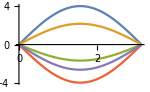
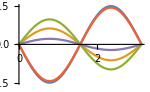
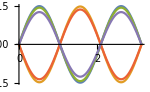
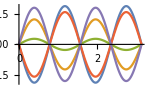

```mathematica
Table[Show[Plot[Table[asol[x,t][[m]],{t,0,4}]//Evaluate,{x,0,Pi},Ticks->False],ImageSize->150],{m,4}]
```

```mathematica
Animate[Plot[asol[x,t],{x,0,π},PlotRange->{-5,5},ImageSize->Medium,PlotStyle->Green],{t,0,2 Pi},SaveDefinitions->True]
```

```mathematica
(* Note : In the above wave equation the length of the string is considered Π (Pi).*)
```